## Function to Solve Schrödinger’s Equation

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]]
findEvolutionOperator[Hin_, Tmax_?NumericQ, acc_:10]:=(
funcs=Array[ψ[#2 + Length[Hin]*(#1- 1)][t]&,{Length[Hin],Length[Hin]}];
equations=Flatten@Join[Thread[Hin.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[Length[Hin]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]], MaxSteps->10^6]
)
```

## Driving with 1/2 the Transition Frequency

This is a toy model of the nuclear spin qubit in the {|g↓⇓⟩, |e↓⇓⟩} subspace.  It’s just the Rabi model with an extra σ_z driving term.  When the frequency equals the transition energy (ω = Δ) there are rapid oscillations which quickly subside as the frequency is changed.  Weirdly, though, there are strong oscillations when ω = Δ/2.

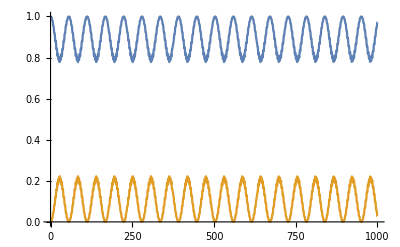

```mathematica
Ω = .05;
Δ = 1;
ω = Δ/2;
Tmax = 1000;
H = {{-Ω*Cos[ω*t], Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ + Ω*Cos[ω*t]}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```

These oscillations can actually be made into complete transitions by shifting the frequency slightly!  I’m not sure how to derive that shift yet, but I can approximate it with Floquet theory.

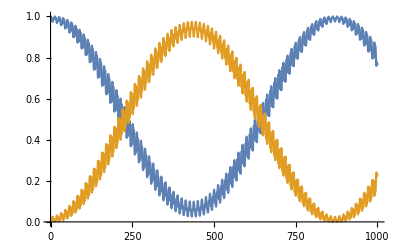

```mathematica
Ω = .05;
Δ = 1;
ω = Δ/2 + .0018;
Tmax = 1000;
H = {{-Ω*Cos[ω*t], Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ + Ω*Cos[ω*t]}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```

## Driving with 1/3 Transition Frequency

The weirder thing is that even just the plain Rabi model can be driven with a frequency near Δ/3.  I think this should work with any odd integer, but it’d keep getting slower.

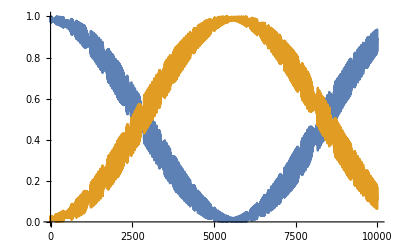

```mathematica
Ω = .1;
Δ = 1;
ω = Δ/3 + 0.0037592;
Tmax = 10000;
H = {{0, Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```

```mathematica
Clear[mTP]
mTP[δ_?NumericQ] := (
Ω = .1;
Δ = 1;
ω = Δ/3 + δ;
Tmax = 10000;
H = {{0, Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ}};
U = findEvolutionOperator[H, Tmax];

tProb[t_?NumericQ] := Abs[U[[1, 2]]]^2;
maxTProb = NMaximize[tProb[t], {t, 0, Tmax}, Method->{"RandomSearch", "SearchPoints"->1000}][[1]];
Print[{δ, maxTProb}];
Pause[1];
maxTProb
)

NMaximize[{mTP[δ], -.02<δ<.02}, {δ, .004, .005}, Method->"NelderMead"]

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]

(*HF = {{-3ω, 0, 0, Ω, 0, 0, 0, 0}, {0, Δ-3ω, Ω, 0, 0, 0, 0, 0}, {0, Ω, -2ω, 0, 0, Ω, 0, 0}, {Ω, 0, 0, Δ-2ω, Ω, 0, 0, 0}, {0, 0, 0, Ω, -ω, 0, 0, Ω}, {0, 0, Ω, 0, 0, Δ-ω, Ω, 0}, {0, 0, 0, 0, 0, Ω, 0, 0}, {0, 0, 0, 0, Ω, 0, 0, Δ}};
statesInOrder[HF] // MatrixForm*)
```

{0.00404573,0.456194}

{0.00403065,0.479583}

{0.00401558,0.500222}

{0.0040005,0.526109}

{0.00397034,0.58037}

{0.00394019,0.640228}

{0.00387988,0.787745}

{0.00381956,0.936242}

{0.00369894,0.964136}

{0.00357832,0.562001}

{0.00357832,0.562001}

{0.00375925,1.}

{0.00381956,0.936242}

{0.0037291,0.999}

{0.00378941,0.98586}

{0.00374418,0.999933}

{0.00377433,0.998099}

{0.00375171,0.999342}

{0.00375925,1.}

{0.00375171,0.999342}

{0.00376679,0.99994}

{0.00376302,0.999922}

{0.00375548,0.999739}

{0.00376114,0.999919}

{0.00375925,1.}

{0.00376114,0.999919}

{0.00375737,0.999932}

{0.00375831,0.999984}

{0.0037602,0.99998}

{0.00375878,0.999997}

{0.00375972,0.999995}

{0.00375902,1.}

{0.00375949,0.999999}

{0.00375914,1.}

{0.00375937,1.}

{0.00375919,1.}

{0.00375914,1.}

{0.00375922,1.}

{0.00375925,1.}

{0.00375921,1.}

$Aborted

$Aborted

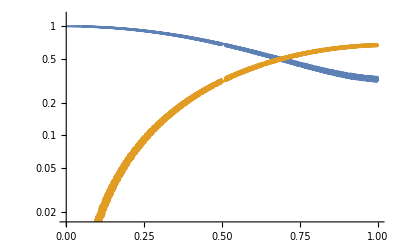

```mathematica
findEvolutionOperator[{{-3.3085980497378742*^10-9.109614822905365*^8 Cos[3.3085980497378742*^10 t],-0*5.834331929262962*^7+9.109614822905365*^8 Cos[3.3085980497378742*^10 t]},{-0*5.834331929262962*^7+9.109614822905365*^8 Cos[3.3085980497378742*^10 t],3.3085980497378742*^10+9.109614822905365*^8 Cos[3.3085980497378742*^10 t]}}, 10^-7];
Evaluate@Table[Max[Abs[%[[i]][[1]]]^2, 10^-8], {i, 2}];
pE1 = LogPlot[{%[[1]], %[[2]]}, {t, 0,  10^-7}]
```

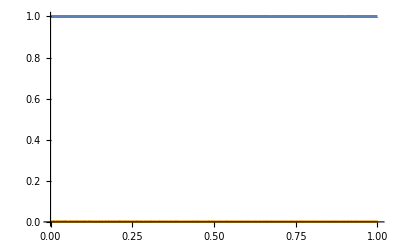

```mathematica
A = 9.109614822905365*^8;
Δ = 2*3.3085980497378742*^10;
B = 0;
ω = Δ/2 + 0;
Tmax = 10^-7;
H = {{2*A*Cos[ω*t], A*Cos[ω*t] + B}, {A*Cos[ω*t] + B, Δ + 2*A*Cos[ω*t]}};
U = findEvolutionOperator[H, Tmax];

(*HF={{-2ω, B, 0, A, 0, 0}, {B, Δ-2ω, A, 0, 0, 0}, {0, A, -ω, B, 0, A}, {A, 0, B, Δ-ω, A, 0}, {0, 0, 0, A, 0, B}, {0, 0, A, 0, B, Δ}};
Eigensystem[HF] // MatrixForm*)

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```